```mathematica
V0=1;
Tmax=0.1;
DiamP=8;
Nmax=128;
E0=0;
```

```mathematica
FV[j_,n_,V0_]:=V0*Sqrt[2*Pi]*Sum[(DiscreteDelta[k-j]-DiscreteDelta[k+j])/2/I/k,{k,1,n}];
A[n_]:=Table[Sum[1/k,{k,1,m}],{m,1,n}];
P[n_]:=Table[1/k/A[n][[n]],{k,1,n}]/2;
(* n = 4 *)
Print["kappa = ",kappa=A[4][[4]]];
m2=2*Sum[P[4][[k]]*k^2,{k,1,Length[P[4]]}];
R[t_]=4*Sqrt[m2*kappa*t];
RC=R[Tmax];
h=(RC+DiamP)/Nmax;
E0Shift=IntegerPart[E0*Tmax/h];
```

kappa = 25/12

```mathematica
Stream=OpenRead["/home/zoldatoff/MSU/matrix/matrix.dat"];
Mat=Read[Stream];
Close[Stream];
```

OpenRead::noopen: Cannot open /home/zoldatoff/MSU/matrix/(*
StyleBox[(*
 StyleBox[
  StyleBox[
   StyleBox["m".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

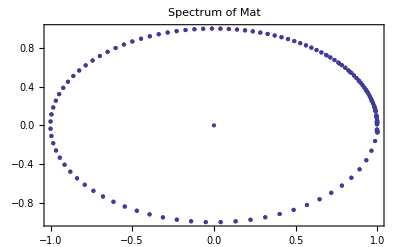

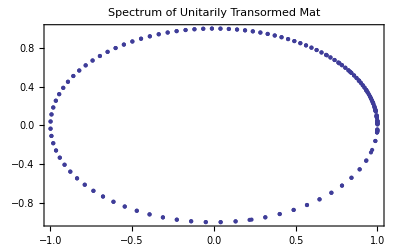

```mathematica
(* Спектр Mat должен лежать вблизи единчной окружности *)
Ed=IdentityMatrix[Length[Mat]];

EigM=Eigenvalues[Mat];
SpM=Table[{Re[EigM[[k]]],Im[EigM[[k]]]},{k,1,Length[Mat]}];

SpecM=ListPlot[SpM,Frame->True,PlotLabel->"Spectrum of Mat",
    PlotRange->All]
    
    (* Унитаризация разрешающего опратора и оценка спектра *)
CMat=Conjugate[Transpose[Mat]];
EU=Inverse[Ed+Mat];
EUC=Inverse[Ed+CMat];
H=0.5*I*((Ed-Mat).EU-(Ed-CMat).EUC);
U=(Ed+I*H).Inverse[Ed-I*H];
EigU=Eigenvalues[U];

SpU=Table[{Re[EigU[[k]]],Im[EigU[[k]]]},{k,1,Length[U]}];

SpecU=ListPlot[SpU,Frame->True,
      PlotLabel->"Spectrum of Unitarily Transormed Mat",
      PlotRange->All]
```

# Отбор для Mat по мининуму L_ 2 нормы производной - РАБОТАЕТ, НО НЕ ОЧЕНЬ!

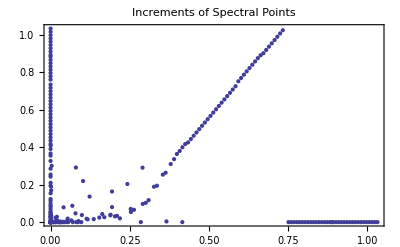

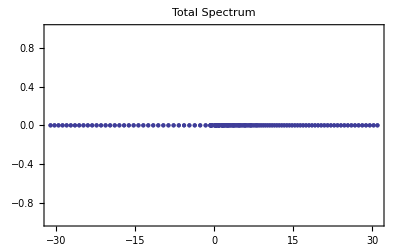

```mathematica
(* Факторизация собстевенных значений  mod(2 * Pi * E0) *)      
EngEv=Arg[EigM]/Tmax;
SE=Sort[EngEv];
DSE=Table[SE[[k+1]]-SE[[k]],{k,1,Length[SE]-1}];

ListPlot[Table[{DSE[[k]],Sort[DSE][[k]]},{k,1,Length[DSE]}],Frame->True,PlotLabel->"Increments of Spectral Points",PlotRange->All]

(*EV=Select[EngEv,And[#>=-kappa,#<=kappa]&]
If[EV=={},Print["No approximate ground eigenvalue has been found!"]]
Spectrum=Table[{EV[[k]],0},{k,1,Length[EV]}]; *)

(*  L - Факторизация спектра для Mat. *)
(*Print["Expected period of the spectrum  L = 2*Pi*E0 =",L=2*Pi*E0];


Spectrum=Table[{Mod[EngEv[[k]],L],0},{k,1,Length[EngEv]}];
ListPlot[Spectrum,Frame->True,PlotLabel->StyleForm["L-Factorization of the Spectrum"],PlotRange->All,PlotStyle->{RGBColor[0,0,1],PointSize[0.01]}];  *)
    
ListPlot[Table[{Sort[EngEv][[k]],0},{k,1,Length[EngEv]}],Frame->True,PlotLabel->"Total Spectrum",PlotRange->All]
```

```mathematica
(* Вычисление собственных векторов ψ(p) MC -аппроксимации состояний дискретного спектра и их нормировка*)
ESys=Eigensystem[Mat];
State=ESys[[2]];
Print["L_2 норма  MC-аппроксимаций состояний дискретного спектра = ", NormMC=Sqrt[Sum[Abs[State[[1,n]]]^2,{n,1,Length[Mat]}]*h]];
```

L_2 норма  MC-аппроксимаций состояний дискретного спектра = 0.306186

Сортированные L_2-нормы производной модуля MC -аппроксимаций состояний дискретного спектра и их номера

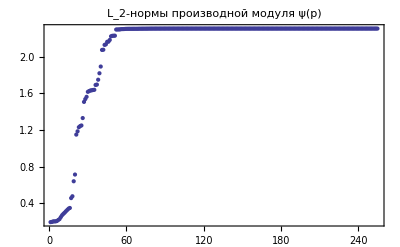

{1,6,3,2,4,139,5,248,37,251,94,200,249,11,254,253,252,225,250,132,211,218,219,213,178,223,214,217,224,8,212,255,237,226,227,93,220,222,216,9,67,10,26,89,210,207,7,23,221,209,16,148,203,205,147,208,48,173,170,229,201,198,199,204,150,141,193,206,202,247,235,236,159,114,111,188,13,215,122,149,190,197,129,169,182,196,179,105,21,152,22,155,63,86,41,59,53,186,161,189,39,195,234,156,192,126,163,44,14,12,232,165,38,51,17,19,231,157,185,184,183,153,167,145,125,130,180,158,176,175,142,174,138,135,171,116,154,118,127,166,124,162,160,121,244,113,151,110,146,106,108,144,103,140,241,136,100,97,134,92,131,88,123,128,34,85,120,81,117,78,115,74,112,50,70,109,57,91,65,46,54,107,61,104,96,101,233,99,43,87,30,27,40,68,83,28,36,79,33,75,71,66,18,24,62,35,58,82,55,32,143,133,25,29,77,119,73,137,69,64,15,60,20,56,194,52,191,47,31,49,187,45,42,102,181,98,177,95,90,172,84,168,80,76,164,72,246,228,243,245,230,242,238,240,239}

{0.194419,0.196549,0.202154,0.202622,0.202991,0.206996,0.217881,0.227989,0.249889,0.270563,0.285335,0.2987,0.313709,0.327609,0.341632,0.349095,0.457107,0.477188,0.640955,0.714445,1.15077,1.1866,1.2316,1.24378,1.25068,1.33164,1.50819,1.53894,1.56372,1.61836,1.62625,1.63299,1.63485,1.6382,1.64026,1.69331,1.69745,1.75067,1.82108,1.89453,2.07592,2.07804,2.13112,2.13708,2.16479,2.16624,2.18489,2.22482,2.23003,2.2314,2.23148,2.29916,2.29946,2.29987,2.30056,2.30351,2.30386,2.30415,2.30564,2.30638,2.30662,2.30676,2.30686,2.30692,2.30697,2.30709,2.3071,2.30712,2.30714,2.3079,2.3079,2.30799,2.30818,2.30824,2.30826,2.30831,2.30859,2.30885,2.3089,2.30897}

```mathematica
Print["Сортированные L_2-нормы :043f:0440:043e:0438:0437:0432:043e:0434:043d:043e:0439 модуля MC -аппроксимаций состояний дискретного спектра и их номера "]; 

NormDMC=Table[Sqrt[Sum[(Abs[State[[k,n-1]]]-Abs[State[[k,n+1]]])^2,{n,2,Length[Mat]-1}]],{k,1,Length[Mat]}]/NormMC/2;

ListPlot[SN=Sort[NormDMC],PlotRange->All,PlotLabel->StyleForm["L_2-нормы :043f:0440:043e:0438:0437:0432:043e:0434:043d:043e:0439 модуля ψ(p)"],Frame->True]
(* Порядок собственных векторов по убыванию нормы *)
ON=Ordering[NormDMC]
(*Первые 80 L_2-норм  производной модуля ψ(p)*)
Table[SN[[k]],{k,1,80}]
```

```mathematica
(*Интерполяция вещественной и мнимой части, модуля и аргумента *)
PsiMC[k_]:=Interpolation[Table[{(n+1)*h-DiamP-RC, Re[State[[k,n]]]/NormMC},{n,1,Length[Mat]}]];

IPsiMC[k_]:=Interpolation[Table[{(n+1)*h-DiamP-RC, Im[State[[k,n]]]/NormMC},{n,1,Length[Mat]}]];

APsiMC[k_]:=Interpolation[Table[{(n+1)*h-DiamP-RC, Abs[State[[k,n]]]/NormMC},{n,1,Length[Mat]}]];

FPsiMC[k_]:=Interpolation[Table[{(n+1)*h-DiamP-RC, Arg[State[[k,n]]]},{n,1,Length[Mat]}]];

XPsi[k_,x_]:=Sum[State[[k,n]]*Exp[I*((n+1)*h-DiamP-RC)*x],{n,1,Length[Mat]}]*h/Sqrt[2*Pi];
```

k = 1; λ = -0.697594

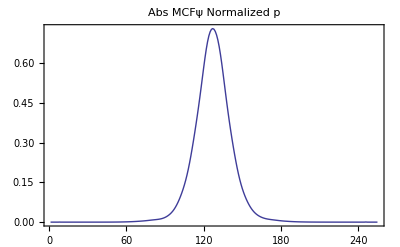

k = 2; λ = -0.729803

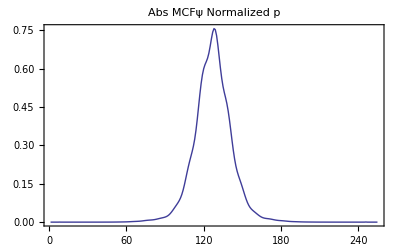

k = 139; λ = -0.622907

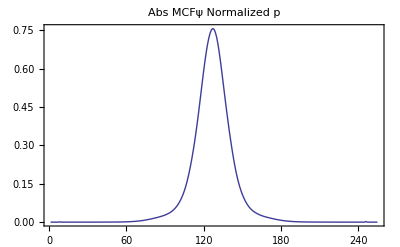

Null^2

```mathematica
(* Ручной выбор вариантов среди кандидатов в списке норм первой производной и интерполяция графика *)
cand={1,4,6};
Do[{
Print["k = ",j=ON[[cand[[k]]]],"; λ = ",EngEv[[j]]];
Print[ListPlot[Abs[State[[j]]]/NormMC,Frame->True,PlotRange->All,PlotLabel->Normalized Abs MCFψ(p), PlotJoined->True]];
(*Print["|ψ(x)| in X-representation at x0 = ",x0=(Arg[State[[j,127]]]-Arg[State[[j,128]]])/h];
Print[Plot[Abs[XPsi[j,x]],{x,x0-10,x0+10},PlotRange->All,Frame->True]];*)
},
{k,1,Length[cand]}]
```

Num of Ev = 2;   λ = -0.700015

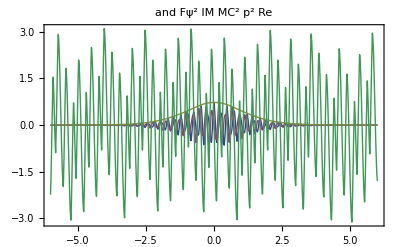

Num of Ev = 3;   λ = -0.730047

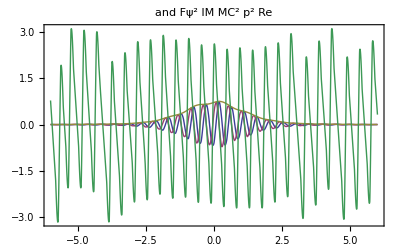

Num of Ev = 1;   λ = -0.732376

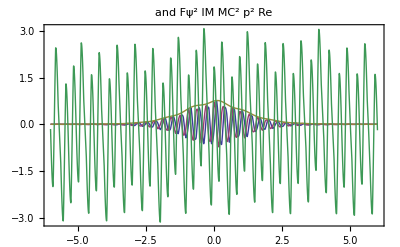

```mathematica
Needs["PlotLegends`"]
Do[{
Print[" Num of Ev = ",cj=ON⟦cand⟦j⟧⟧,";   λ = ",EngEv⟦cj⟧],
Print[Plot[
{PsiMC[cj][p],IPsiMC[cj][p],APsiMC[cj][p],FPsiMC[cj][p]},
{p,-6,6},
Frame->True,PlotRange->All,PlotLabel->Re MC Fψ(p) and  IM MC Fψ(p),PlotLegend->{"Re MCFφ[p]","Im MCFφ[p]","Abs MCFφ[p]","Arg MCFφ[p]"}]
]},
{j,1,Length[cand]}]
```

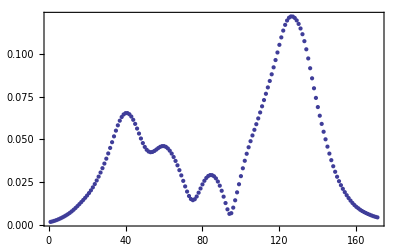

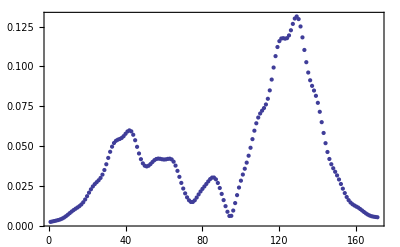

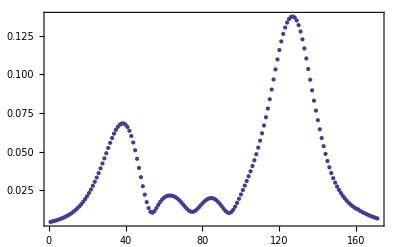

```mathematica
(* Оценка погрешности вычислений в уравнении (H - λ)Fψ = 0 для решений из списка cand *)
(*Оценка погрешности для решения,построенного по матрице Mat*)
err[k_]:=Table[(((n+1)*h-DiamP-RC)^2/2-EngEv[[k]])*State[[k,n]]-I*E0*(State[[k,n+1]]-State[[k,n-1]])/2/h-
1/Sqrt[2*Pi]*Sum[Sum[If[Abs[j*h-i]<h/2,FV[i,4,V0],0],{i,-4,4}]*State[[k,-j+n]],{j,-IntegerPart[RC/h],IntegerPart[RC/h]}], {n,IntegerPart[RC/h]+1,Length[Mat]-IntegerPart[RC/h]}]/NormMC;

Do[
k=ON[[cand[[j]]]];
Print[ListPlot[Abs[err[k]],Frame->True,PlotRange->All]];
, {j,1,Length[cand]}];
```

# Отбор для Mat по инимальной дисперсии | p | - РАБОТАЕТ!

```mathematica
Print["Сортирвка дисперсии модуля MC -аппроксимаций состояний дискретного спектра и их номера "]; 

MeanP=Table[Sum[Abs[State[[k,n]]]^2*(n*h-DiamP-RC),{n,1,Length[U]}],{k,1,Length[U]}]/NormMC;
DispP=Table[Sum[Abs[State[[k,n]]]^2*(n*h-DiamP-RC-MeanP[[k]])^2,{n,1,Length[U]}],{k,1,Length[U]}]/NormMC;
SN=Sort[DispP]
ON=Ordering[DispP]
```

Сортирвка дисперсии модуля MC -аппроксимаций состояний дискретного спектра и их номера

{1.1032,1.32308,1.40492,1.7678,1.78375,2.04237,2.06777,2.20228,2.23112,2.28363,2.29612,2.89015,2.90429,3.30249,3.59726,3.69995,3.77453,3.79952,3.93976,3.94862,4.31101,4.71619,4.88749,4.97164,5.03593,5.06884,5.58866,6.75367,6.9906,7.08903,7.16936,7.31553,7.32868,7.41609,7.5258,8.11002,8.33609,12.2255,12.2295,12.7386,13.0837,13.45,15.0735,19.3252,20.437,20.7328,23.7222,29.7865,29.8548,30.6997,39.0854,39.1429,50.779,53.9268,54.9469,56.941,59.5194,60.3908,69.6696,69.9697,77.6598,82.3199,91.0426,99.0702,110.764,114.25,120.067,127.099,128.544,133.743,137.068,145.731,146.39,157.898,162.02,168.096,177.429,177.749,178.444,188.238,199.197,211.13,222.724,233.717,234.362,245.494,245.867,258.16,270.596,271.292,284.184,296.902,297.362,310.397,310.829,324.177,338.244,338.626,352.977,367.242,367.61,382.191,382.535,396.549,397.422,409.778,412.944,424.792,428.156,429.062,441.332,445.158,461.264,461.546,477.956,478.227,487.242,490.013,494.94,503.283,512.207,512.47,523.553,530.032,547.652,547.887,565.809,566.036,584.259,584.333,602.98,603.215,621.933,622.246,641.371,641.571,660.996,661.19,680.915,681.102,701.127,701.305,721.589,721.81,742.43,742.606,763.53,763.695,784.919,785.08,806.599,806.756,819.494,828.73,841.34,850.846,850.997,873.415,873.558,896.275,896.414,915.606,919.429,919.565,943.009,966.601,966.749,990.658,990.783,1014.99,1015.11,1039.62,1039.86,1051.01,1063.75,1064.6,1089.81,1115.03,1115.32,1140.84,1141.12,1166.94,1167.21,1193.32,1193.6,1220.28,1246.98,1247.26,1258.38,1274.25,1274.53,1301.8,1302.1,1329.63,1330.18,1358.06,1370.33,1386.51,1414.42,1415.26,1443.37,1444.3,1472.5,1473.63,1500.31,1503.26,1533.18,1561.12,1563.4,1590.52,1593.91,1618.03,1622.04,1624.72,1631.8,1656.09,1687.1,1691.6,1718.79,1739.46,1750.78,1771.3,1783.06,1792.25,1815.63,1846.65,1848.5,1881.66,1887.86,1896.31,1912.09,1915.12,1929.26,1948.88,1952.6,1960.13,1982.95,1983.13,2016.5,2051.13,2051.98,2052.06,2086.05,2121.3,2156.77,2156.83,2192.65,2202.75,2228.76,2265.17,2291.47,2301.73,2338.87,2347.17,2377.27}

{249,251,173,238,6,4,47,2,5,1,3,254,252,253,250,215,199,225,78,158,217,211,212,209,130,213,214,223,224,8,221,219,218,143,222,9,12,7,110,139,208,220,70,210,56,204,206,24,216,66,197,53,194,132,146,195,207,155,202,203,205,200,201,177,193,154,196,174,198,179,184,182,190,189,153,191,166,127,192,169,170,188,187,162,186,185,161,157,152,183,180,148,178,144,175,141,138,171,168,133,165,128,163,160,125,156,122,113,119,150,117,149,114,145,111,140,18,137,107,48,105,135,102,131,99,126,96,123,93,121,90,118,87,115,84,112,81,109,76,106,73,103,68,100,63,97,59,94,54,91,49,88,44,85,108,41,80,38,75,35,72,29,32,67,62,26,58,22,51,19,46,16,83,34,37,79,74,31,69,28,64,25,60,21,55,50,15,45,27,13,42,11,39,10,95,92,43,89,40,86,36,82,33,77,30,71,65,23,61,20,57,17,134,52,14,181,176,129,172,124,167,120,164,116,159,231,151,147,104,236,229,142,101,136,98,234,235,248,247,246,233,232,245,244,230,243,242,228,241,240,227,239,237,226,255}

k = 249; λ = -0.416366

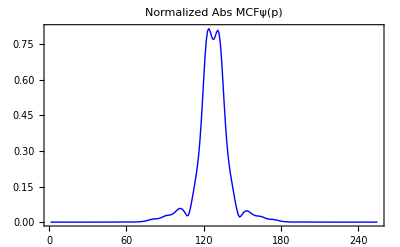

k = 238; λ = -0.535697

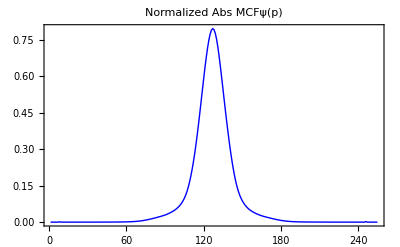

k = 1; λ = -0.732376

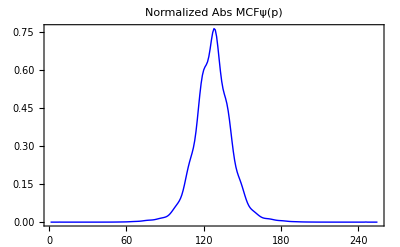

```mathematica
(* Ручной выбор вариантов среди кандидатов в списке дисперсии и интерполяция графика *)
cand={1,4,10}; 
Do[{
Print["k = ",j=ON[[cand[[k]]]],"; λ = ",EngEv[[j]](*, ";  λ(mod L) = ",Mod[EngEv[[j]],L]*)];
Print[ListPlot[Abs[State[[j]]]/NormMC,
Frame->True,PlotRange->All, PlotLabel->"Normalized  Abs MCFψ(p)",PlotJoined->True,PlotStyle->{RGBColor[0,0,1]}]];
(*
Print["|ψ(x)| in X-representation at x0 = ",x0=(Arg[State[[j,127]]]-Arg[State[[j,128]]])/h];
Print[Plot[Abs[XPsi[j,x]],{x,x0-10,x0+10},PlotRange->All,Frame->True]]
*)
(*;
Print["Arg[ψ(x)] in X-representation at x0 = ",x0];
Plot[Arg[XPsi[j,x]],{x,x0-6,x0+6},PlotRange->All,Frame->True]*)
},
{k,1,Length[cand]}];
   
(*Do[{Print["k = ",ON[[cand[[k]]]],"; λ = ",EngEv[[ON[[cand[[k]]]]]], ";  λ(mod L) = ",Mod[EngEv[[ON[[cand[[k]]]]]],L]];ListPlot[Arg[State[[ON[[cand[[k]]]]]]],Frame->True,PlotRange->All, PlotLabel->StyleForm[" Arg MCFψ(p)"],
      DefaultFont->{"Courier",14},
   PlotStyle->{RGBColor[1,0,0]}]},{k,1,Length[cand]}];   *)
```

k = 249;    λ = -0.416366

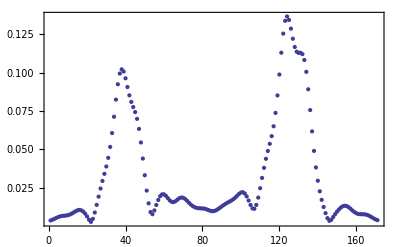

k = 238;    λ = -0.535697

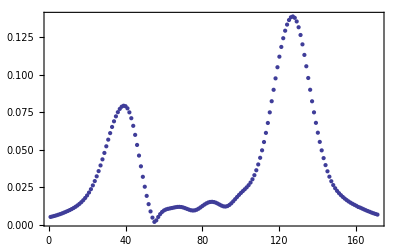

k = 1;    λ = -0.732376

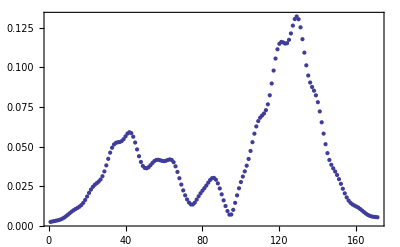

```mathematica
(* Оценка погрешности для решения, построенного отбором по дисперсии для  матрицы Mat *)
err[k_]:=Table[(((n+1)*h-DiamP-RC)^2/2-EngEv[[k]])*State[[k,n]]-I*E0*(State[[k,n+1]]-State[[k,n-1]])/2/h-
1/Sqrt[2*Pi]*Sum[Sum[If[Abs[j*h-i]<h/2,FV[i,4,V0],0],{i,-4,4}]*State[[k,-j+n]],{j,-IntegerPart[RC/h],IntegerPart[RC/h]}], {n,IntegerPart[RC/h]+1,Length[Mat]-IntegerPart[RC/h]}]/NormMC;

Do[{
k=ON[[cand[[j]]]];
Print["k = ",k,";    λ = ",EngEv[[k]](*, ";  λ(mod L) = ",Mod[EngEv[[k]],L]*)];Print[ListPlot[Abs[err[k]],Frame->True,PlotRange->All]]},
{j,1,Length[cand]}
]
```